## Zestaw 2

### Zadanie 2

### a) Rozkład eksponencjalny

Dla rozkładu eksponencjalnego rachunki wykonano ręcznie (zdjęcie załączone)

```mathematica
Import["C:\\Users\\wojci\\Desktop\\Studia\\V rok\\Semestr letni\\Risk Menagement\\Set2\\img\\2-21.jpg", "jpg"]
```

-Graphics-

```mathematica
Rotate[Import["C:\\Users\\wojci\\Desktop\\Studia\\V rok\\Semestr letni\\Risk Menagement\\Set2\\img\\2-22.jpg", "jpg"],Pi/2]
```

-Graphics-

```mathematica
λ=1;
```

#### VaR(X) = ln(1-α)/λ

```mathematica
VaRa[a_] = 1/λ * Log[1-a];
```

Wykres zależności VaR(X) dla rozkładu eksponencjalnego

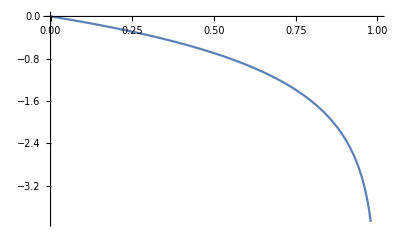

```mathematica
a1=Plot[VaRa[a], {a,0,1}]
```

#### ES(X) =- [1-((α-1)/α)ln(1-α)]/λ

Wykres zależności ES(X) dla rozkładu eksponencjalnego

```mathematica
ESa[a_] = -1/λ * (1-(a-1)/a *Log[1-a]);
```

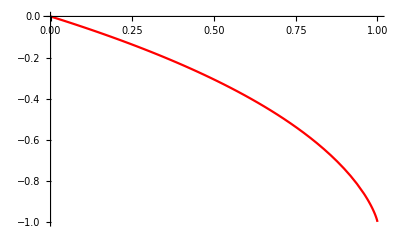

```mathematica
a2=Plot[ESa[a],{a,0,1},PlotStyle->Red]
```

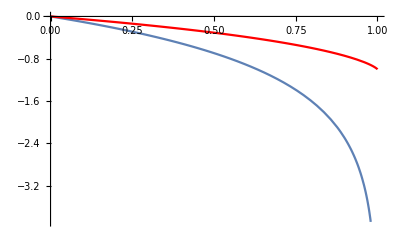

```mathematica
Show[{a1,a2}]
```

Kolorem czerwonym zaznaczono Expected Shortfal

#### W powyższych rozwiązaniach zastanawiającym jest to, że VaR_α i ES_α okazują się być rosnącymi a nie malejącymi funckjami α. Może to wynikać z błędnego znaku przy wyliczaniu VaR_α

### b) Rozkład normalny

PDF rozkładu normalnego przyjmuje postać jak poniżej

P[x_] = 1/(σ Sqrt[2Pi])Exp[(-(x-μ))/(2σ^2)];

Policzenie VaR_α w tym przypadku jest trudne ,,na kartce’’ ze względu na obecność funcji specjalnych, dlatego rozwiązanie zostanie wykonane tutaj, w programie do obliczeń symbolicznych.

Jeśli przyjmiemy definicję VaR_α postaci
α = (∫^-VaR)_(-∞) P(x)ⅆx
które to wyrażenie jest definicją kwantyla rzędu α to VaR będzie ,,minus kwantylem rzędu α’’. A ten z kolei może być policzony jako

```mathematica
Quantile[NormalDistribution[μ,σ],α]
```

-0.31398

Jest to wyrażenie warunkowe ze względu na wartość α która nie może być mniejsza niż zero ani większa od jedynki. Powyższe wyrażenie zawiera odwrotną funkcję Erfc, czyli funkcję odwrotną do  komplementarnej funkcji błędu: 
Erfc(x) = 1 - Erf(x)

Zatem VaR(X) =  - (μ-√2 σ InverseErfc[2 α])

Co po narysowaniu jako funkcji zmiennej α, z parametrami μ = 0 i σ = 1 ma postać:

```mathematica
μ=0;
```

```mathematica
σ = 1;
```

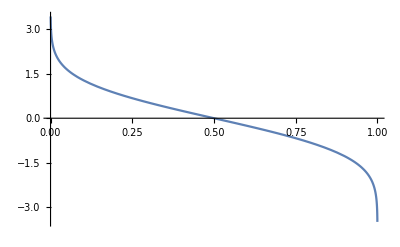

```mathematica
k=Plot[-(μ-√2 σ InverseErfc[2 α]),{α,0,1}]
```

```mathematica
Clear[σ]
```

```mathematica
Clear[μ]
```

ES (X) policzyć można z kolei następująco:
(Wyrażenie to pokrywa się z definicją ES zawartą w treści zadania 1)

```mathematica
ESb[α] = 1/α * Integrate[-(μ-√2 σ InverseErfc[2 γ]),{γ,0,α}]
```

52 (-μ/52+(ⅇ^(-InverseErfc[1/26]^2) σ)/(√(2 π)))

Wyrażenie to ponownie zależy od funkcji odwrotnej do komplementarnej funkcji błędu i po ustaleniu wartości parametrów jego wykres to :

```mathematica
μ=0;
```

```mathematica
σ = 1;
```

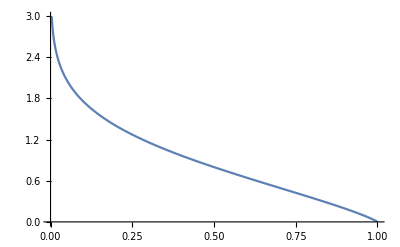

```mathematica
es2=Plot[(-α μ+(ⅇ^(-InverseErfc[2 α]^2) σ)/(√(2 π)))/α,{α,0,1}]
```

Aby zweryfikować poprawność powyższych formuł  rachunek wykonałem korzystając z innych funkcji:

```mathematica
Import["C:\\Users\\wojci\\Desktop\\Studia\\V rok\\Semestr letni\\Risk Menagement\\Set2\\img\\2-2b.jpg", "jpg"]
```

-Graphics-

A następnie narysowałem jej wykres VaR

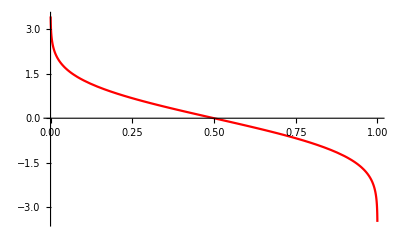

```mathematica
aa = Plot[-(μ+InverseErf[2α-1]*Sqrt[2] )*σ,{α,0,1},PlotStyle->Red]
```

I nałożyłem wykresy liczone dwoma sposobami na siebie

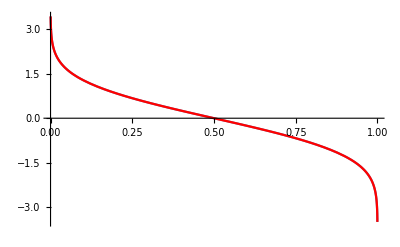

```mathematica
Show[{k,aa}]
```

Jak widać zupełnie się przekrywają, co stanowi o równoważności tych podejść

Następnie, dla ES

```mathematica
Clear[σ]
```

```mathematica
Clear[μ]
```

```mathematica
ESb2 = Integrate[-1*(μ+Sqrt[2]*σ*InverseErf[2γ-1]),{γ,0,α}]/α
```

52 (-μ/52+(ⅇ^(-InverseErf[25/26]^2) σ)/(√(2 π)))

```mathematica
μ=0;
```

```mathematica
σ = 1;
```

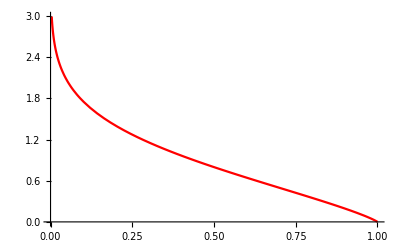

```mathematica
es1=Plot[(-α μ+(ⅇ^(-InverseErf[-1+2 α]^2) σ)/(√(2 π)))/α,{α,0,1},PlotStyle->Red]
```

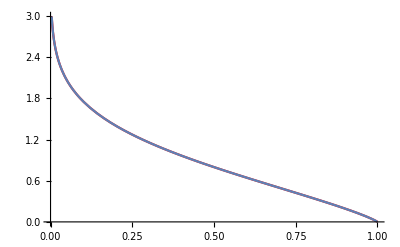

```mathematica
Show[{es1,es2}]
```

Również dla ES obydwa sposoby liczenia są równoważne

## Zadanie 3.

W zadaniu tym korzystamy z modelu, w którym wartość pewnego instrumentu finansowego w chwili t (S(t)) ma rozkład normalny, przy czym korzystamy z uproszczonej formuły opisującej zależność S(t) od pozostałych parametrów modelu i pewnej zmiennej losowej ξ o rozkładzie normalnym: N(0,1).

S(t) = S(0)  + S(0) μ t  = S(0) σ Sqrt[t] ξ,
gdzie S(0) to bieżąca cena (zainwestowany kapitał), μ jest oczekiwaną stopą zwrotu , σ to volatility a t jest interwałem czasowym. 
To co warto tutaj zaznaczyć, w tym modelu volatility nie jest zdefiniowane za Wykładem jako odchylenie standardowe zmiennej losowej x = ln((S(t))/(S(0))), tylko przyjmujemy je jako parametr σ zawarty w powyższym równaniu.

Bazując na tym modelu chcemy wyznaczyć VaR_α(X), oraz ES_α(X). W tym celu  musimy wpierw skonstruować zmienną losową X, którą zdefiniujemy za Wykładem jako
X = ΔS = S(t) - S(0) = S(0) μ t  + S(0) σ Sqrt[t] ξ
Można zauważyć, że zmienna ta ma rozkład normalny N(m, s), gdzie
m = S(0) μ t
s = S(0) σ Sqrt[t]

### a) Wyprowadź funkcyjną relację pomiędzy volatility σ, VaR_α i ES_α

W świetle powyższej dyskusji (i bazując na wynikach poprzedniego zadania) możemy zapisać

```mathematica
Clear[σ]
```

```mathematica
Clear[μ]
```

#### VaR_α

```mathematica
VaR3a = -(m-√2 s InverseErfc[2 α]);
```

A skoro

```mathematica
m = S0 μ t;
s = S0 σ Sqrt[t];
```

to

```mathematica
VaR3a
```

5.54857

Tym co szczególnie zasługuje na uwagę jest fakt, że zależność Value at Risk  i volatility jest liniowa

#### ES_α

Wstawiając wyniki poprzedniego zadania i podstawiając odpowiednie wyrażenia za m i s otrzymujemy

```mathematica
ES3a = - m+(ⅇ^(-InverseErf[-1+2 α]^2) s)/(α √(2 π))
```

-(25 μ)/13+100 ⅇ^(-InverseErf[25/26]^2) √(26/π) σ

Okazuje się tutaj, że także zależność między Expected Shortfall a volatility jest liniowa

```mathematica
Clear[σ]
```

```mathematica
Clear[μ]
```

```mathematica
Clear[s]
```

```mathematica
Clear[m]
```

### b) Obliczyć ,,dzienne’’ VaR_α i ES_α dla akcji, któych ceny mają rozkład gaussowski opisany przez powyższe równanie.

W tym podpunkcie parametry rozpatrywanego modelu to

```mathematica
S0 = 100;
```

, ,Roczna’’ oczekiwana stopa zwrotu

```mathematica
μ = 0.1;
```

,,Roczne’’ volatility:

```mathematica
σ = 0.2;
```

Zakładamy, że rok ma 250 dni roboczych, oraz że istnieje możliwość zaobserwowania strat większych niż VaR_α tylko 1 raz w ciągu roku, co stanowi, że

```mathematica
α = 1/250;
```

Ponadto ,,dzienne’’ rozpatrywany  czas to

```mathematica
t = 1/250;
```

Wtedy

```mathematica
m = S0 μ t;
s = S0 σ Sqrt[t];
```

Co daje wyniki , , dzienne''

```mathematica
VaR3b = -(m-√2 s InverseErfc[2 α])
```

3.31463

```mathematica
ES3a = - m+(ⅇ^(-InverseErf[-1+2 α]^2) s)/(α √(2 π))
```

3.70637

### c) Obliczyć ,,dzienne’’ VaR_α i ES_α

Ten podpunkt wykonać można analogicznie jak poprzedni, z tą tylko różnicą, że teraz

```mathematica
σ = 0.3;
```

Pozostała część rachunku jest zupełnie analogiczna jak wyżej

```mathematica
μ = 0.1;
```

```mathematica
α = 1/250;
```

```mathematica
t = 1/250;
```

```mathematica
m = S0 μ t;
s = S0 σ Sqrt[t];
```

```mathematica
VaR3c = -(m-√2 s InverseErfc[2 α])
```

4.99195

```mathematica
ES3c = - m+(ⅇ^(-InverseErf[-1+2 α]^2) s)/(α √(2 π))
```

5.57955

### d) Obliczyć ,,dzienne’’ VaR_α i ES_α przy założeniu, że w ciągu roku obserwujemy 2 lub 3 straty powyżej VaR_α. W tym celu należy wybrać odpowiedni poziom ufności α

Ten podpunkt wykonujemy zupełnie analogicznie jak dwa poprzednie. Jedyna różnica tkwi w przyjęciu innej definicji parametru α. Zatem:

```mathematica
μ = 0.1;
```

```mathematica
σ = 0.2;
```

```mathematica
t = 1/250;
```

```mathematica
m = S0 μ t;
s = S0 σ Sqrt[t];
```

Zakładając 2 straty w ciągu roku przekraczające VaR_α

W  "horyzoncie czasowym" jednego roku (250 dni roboczych) dwukrotnie oczekujemy sytuacji, w której straty przekroczą Value at Risk z odpowiednim poziomem ufności, czyli α = 2/250

```mathematica
α = 2/250;
```

```mathematica
VaR3d2 = -(m-√2 s InverseErfc[2 α])
```

3.00706

```mathematica
ES3d2 = - m+(ⅇ^(-InverseErf[-1+2 α]^2) s)/(α √(2 π))
```

3.42579

Zakładając 3 straty w ciągu roku przekraczające VaR_α

```mathematica
α = 3/250;
```

```mathematica
VaR3d3 = -(m-√2 s InverseErfc[2 α])
```

2.81507

```mathematica
ES3d3 = - m+(ⅇ^(-InverseErf[-1+2 α]^2) s)/(α √(2 π))
```

3.25233

### e) Obliczyć ,,dzienne’’ VaR_α i ES_α dla przedziału czasowego 2 lub 3 lata zakładając jedną stratę przekraczającą VaR_α. W tym celu wybierz odpowiednie α

Podpunkt ten jest analogiczny do poprzednich. Zmienia się jedynie horyzont czasowy, w którym obserwujemy straty. Oczekujemy, że w ciągu 2 lub 3 lat zaobserwujemy jedną stratę przekraczającą VaR_α, więc  
i) dla horyzontu czasowego wynoszącego 2 lata: α = 1/(2*250)
ii) dla horyzontu czasowego wynoszącego  lata: α = 1/(3*250)

To co jednak jest tutaj istotne to fakt, że w treści zadania podane są ,,roczne’’ volatility i oczekiwana roczna stopa zwrotu, więc ,,normalizując’’ je aby uzyskać wielkości ,,dzienne’’, należy użyć t = 250 (t wynoszące jeden rok)
Wtedy:

```mathematica
μ = 0.1;
```

```mathematica
σ = 0.2;
```

```mathematica
t = 1/250;
```

```mathematica
m = S0 μ t;
s = S0 σ Sqrt[t];
```

Dla horyzontu czasowego wynoszącego 2 lata

```mathematica
α = 1/500;
```

```mathematica
VaR3e2 = -(m-√2 s InverseErfc[2 α])
```

3.60062

```mathematica
ES3e2 = - m+(ⅇ^(-InverseErf[-1+2 α]^2) s)/(α √(2 π))
```

3.96989

Dla horyzontu czasowego wynoszącego 3 lata

```mathematica
α = 1/750;
```

```mathematica
VaR3e2 = -(m-√2 s InverseErfc[2 α])
```

3.75949

```mathematica
ES3e2 = - m+(ⅇ^(-InverseErf[-1+2 α]^2) s)/(α √(2 π))
```

4.11725

### f) Oblicz ,,tygodniowe’’ VaR_α i ES_α. Wybierz taki poziom ufności α, że oczekujemy w jednym tygodniu straty przekraczającej VaR_α podczas rocznej inwestycji

Zakładam tutaj, że w ciągu roku są 52 tygodnie robocze więc  wykonujemy ,,skalowanie’’ zakładając, że t = 1/52

```mathematica
μ = 0.1;
```

```mathematica
σ = 0.2;
```

```mathematica
t = 1/52;
```

```mathematica
m = S0 μ t;
s = S0 σ Sqrt[t];
```

Skoro oczekujemy 1 straty przekraczającej VaR_α a ustalony przedział czasowy wynosi 1 rok, czyli 52 tygodnie to

```mathematica
α = 1/52;
```

```mathematica
VaR3f = -(m-√2 s InverseErfc[2 α])
```

5.54857

```mathematica
ES3f = - m+(ⅇ^(-InverseErf[-1+2 α]^2) s)/(α √(2 π))
```

6.56192